```mathematica
(* Lets try this test -- integration of a Gaussian using Newton-Cotes rules *)
f[x_]=ⅇ^(-x^2);
xmax=7;
xmin=-xmax;
exact=Integrate[f[x],{x,xmin,xmax}];
Δ = (xmax-xmin)/(nOfPoints-1);

rectangularLeft=Table[{nOfPoints,Δ Sum[f[xmin+Δ (i-1)],{i,1,nOfPoints-1}]},{nOfPoints,3,50}];
rectangularRight=Table[{nOfPoints,Δ Sum[f[xmin+Δ (i-1)],{i,2,nOfPoints}]},{nOfPoints,3,50}];
trapezoidal=Table[{nOfPoints,(f[xmin]+f[xmax])/2 Δ+Δ Sum[f[xmin+Δ (i-1)],{i,2,nOfPoints-1}]},{nOfPoints,3,50}];
N[N[rectangularLeft,20]];
N[N[rectangularRight,20]];
N[N[trapezoidal,20]];
Clear[nOfPoints,array,Δ,xmin,xmax]
rule={x_,y_}->{x,Abs[y-exact]};
rectangularLeftErrors=N[N[rectangularLeft/.rule,20]];
rectangularRightErrors=N[N[rectangularRight/.rule,20]];
trapezoidalErrors=N[N[trapezoidal/.rule,20]];
```

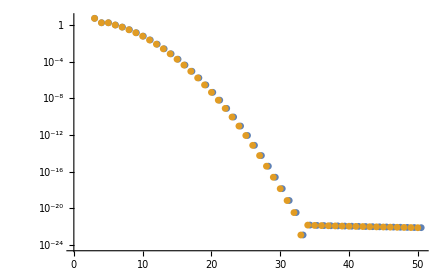

```mathematica
ListLogPlot[{rectangularLeftErrors 1.01,trapezoidalErrors}]
```